```mathematica
Clear["Global`*"]
```

Eigenvalue and Eigenvector Problem - n, m are the cylinder wave numbers

```mathematica
ϕ1=q*a*(1-ν^2)/(Eh*h);
ϕ2=-Nx*(1-ν^2)/(Eh*h);
```

```mathematica
u[θ_,x_]:=A*Sin[n*θ]*Cos[m*Pi*x/L];
v[θ_,x_]:=B*Cos[n*θ]*Sin[m*Pi*x/L];
w[θ_,x_]:=C*Sin[n*θ]*Sin[m*Pi*x/L];
```

```mathematica
goveq1[θ_,x_]:=a^2*D[u[θ,x],{x,2}]+(1+ν)/2*a*D[v[θ,x],{x,1},{θ,1}]-ν*a*D[w[θ,x],x]+a*ϕ1*(D[v[θ,x],{x,1},{θ,1}]-D[w[θ,x],x])+(1-ν)/2*D[u[θ,x],{θ,2}];
goveq2[θ_,x_]:=(1+ν)/2*a*D[u[θ,x],{x,1},{θ,1}]+(1-ν)/2*(a^2)*D[v[θ,x],{x,2}]+D[v[θ,x],{θ,2}]-D[w[θ,x],θ]+α*(D[v[θ,x],{θ,2}]+D[w[θ,x],{θ,3}]+a^2*D[w[θ,x],{x,2},{θ,1}]+a^2*(1-ν)*D[v[θ,x],{x,2}])-a^2*ϕ2*D[v[θ,x],{x,2}];
goveq3[θ_,x_]:=ν*a*D[u[θ,x],x]+D[v[θ,x],θ]-w[θ,x]-α*(D[v[θ,x],{θ,3}]+(2-ν)*a^2*D[v[θ,x],{x,2},{θ,1}]+a^4*D[w[θ,x],{x,4}]+D[w[θ,x],{θ,4}]+2*a^2*D[w[θ,x],{x,2},{θ,2}])-ϕ1*(w[θ,x]+D[w[θ,x],{θ,2}])-ϕ2*a^2*D[w[θ,x],{x,2}];
```

```mathematica
res=Normal@CoefficientArrays[{goveq1[θ,x]/(Cos[m*Pi*x/L]*Sin[n*θ])//TrigReduce,goveq2[θ,x]/(Sin[m*Pi*x/L]*Cos[n*θ])//TrigReduce,goveq3[θ,x]/(Sin[m*Pi*x/L]*Sin[n*θ])//TrigReduce},{A,B,C},"Symmetric"->True]//FullSimplify;
eigarr=res[[2]];
```

Diamond

```mathematica
f=0.003;
L=0.0556;
UBendConPlate=0.3029;
UStretchConPlate=0.05987;
UBendConCyl=3.8189;
UStretchConCyl=1.2915;
uConTop={-4.52666746061424*^-10,0.0187860829953693,-0.000909068719463371,-1.40872858016083*^-09,5.81105026239293*^-10,0.00399965961265028,-0.00039892020738438,1.46891446903438*^-09,-0.00579701031267143,5.38258474061447*^-06,-4.69515433216828*^-08}/1000;
vConTop={1.40385034101728*^-08,0.000912640555292616,0.0187831803270282,-2.46583434893939*^-08,-1.1915819418492*^-09,0.000403955461593803,0.00400322760657658,-3.5850992628408*^-08,-5.39018785952885*^-06,-0.00579746582940801,2.76925402531321*^-08}/1000;
wConTop={-1.78561071194682*^-06,5.03415989410865*^-08,4.59212334356857*^-08,-0.819541911939515,3.72921641344638*^-07,6.87119850951973*^-09,-2.06392485363191*^-08,0.277567424992014,-7.35782306805997*^-09,-4.10440930601307*^-09,0.686449449476511
}/1000;
uConBot={5.2079082675939*^-08,0.0187855139972977,0.00114002125997726,-2.25142231047163*^-07,1.33575335702517*^-07,0.00399965198877464,0.000400779777713704,5.00298644493265*^-08,-0.00579700522678276,-5.94623473127199*^-06,-1.3772200270654*^-08}/1000;
vConBot={-4.56874577171604*^-08,-0.0011366146264199,0.0187830838304798,-1.21243478952719*^-08,-4.43864966509439*^-09,-0.000395741374683266,0.00400316903096333,-6.28892466930405*^-10,5.92538257151489*^-06,-0.00579744375435852,-5.08686873598132*^-08}/1000;
wConBot={1.08869231559976*^-06,-4.63277597670861*^-08,-3.10804061276932*^-08,0.819517059360667,-5.91939643146226*^-07,1.65839193401188*^-08,-1.01612202857077*^-07,-0.277580620576081,1.00265703896763*^-09,4.67554396405172*^-09,-0.397723517941869}/1000;
```

Alternating Ellipse

```mathematica
f=0.003;
L=0.037;
UBendConPlate=0.6547;
UStretchConPlate=1.7635;
UBendConCyl=5.6204;
UStretchConCyl=3.8698;
uConTop={2.76553251128804*^-09,-0.00163785152969084,-1.07652471395914,-7.02228763281459*^-09,8.21849629550079*^-09,-0.0137898987067277,-0.000103506522992816,-8.49464744201965*^-09,-0.014467024847515,-2.73660476122292*^-05,3.34357542478158*^-09}/1000;
vConTop={-1.37754716007638*^-08,1.07647337996753,-0.00157164243557477,9.42354980981884*^-09,6.80617317214054*^-09,0.00010786461126399,-0.0137627580941125,-1.05475369840739*^-08,2.52107524557464*^-05,-0.0144607176129521,-3.15205119166596*^-08}/1000;
wConTop={3.66983011541383*^-05,-5.18989031443941*^-09,-3.95729754140507*^-09,0.0158648763748557,-4.02330079377432*^-05,-9.45500612954753*^-09,-1.59718432283043*^-08,0.532260159451409,-6.39759393168693*^-10,-5.43246311719004*^-10,2.33049650411705}/1000;
uConBot={1.88234703929899*^-09,0.000128093433499063,-1.07653773696874,-5.5267346837947*^-09,1.28315293709375*^-09,-0.013789175030899,0.00040408606331788,-1.02776188231167*^-09,-0.0144666240325943,-5.12329633071596*^-05,4.6389422671888*^-09}/1000;
vConBot={-3.05552210983377*^-09,1.07648446027523,0.000195256545429548,7.75025783355244*^-09,-3.56874286536293*^-09,-0.000399923609970829,-0.013762414405176,1.50568487228396*^-08,4.90159889717118*^-05,-0.0144602989096841,-2.12510956928681*^-08}/1000;
wConBot={-2.79252074127263*^-05,5.17112109872286*^-08,8.72814219001869*^-08,0.0125332623908508,4.0843664969859*^-05,-7.91308968658144*^-09,1.14826830035442*^-08,-0.532272861863801,2.25893373778661*^-09,2.85808274206484*^-10,0.664359825133051}/1000;
```

Set Parameters

```mathematica
n=2;
m=1;
a=0.010;
Eh=0.234*10^6;
ν=0.4995;
h=0.0015;
α=h^2/(12*a^2);
b=0.030;
Nx=q*(b^2-Pi*a^2)/(2*Pi*a);
```

```mathematica
qsol=Solve[Det[eigarr]==0,q];
q=q/.qsol[[1]][[1]];
nullsp=NullSpace[eigarr];
APr=nullsp[[1]][[1]];
BPr=nullsp[[1]][[2]];
CPr=nullsp[[1]][[3]];
```

```mathematica
APr
BPr
CPr
```

0.123752

-0.45977

0.879373

Plate Displacement

```mathematica
up[x_,y_]:=uConBot[[1]]*Sin[Pi*x/b]*Sin[Pi*y/b]+uConBot[[2]]*Sin[Pi*x/b]*Cos[Pi*y/b]+uConBot[[3]]*Cos[Pi*x/b]*Sin[Pi*y/b]+uConBot[[4]]*Cos[Pi*x/b]*Cos[Pi*y/b]+uConBot[[5]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+uConBot[[6]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+uConBot[[7]]*Cos[2*Pi*x/b]*Sin[2*Pi*y/b]+uConBot[[8]]*Cos[2*Pi*x/b]*Cos[2*Pi*y/b]+uConBot[[9]]*x+uConBot[[10]]*y+uConBot[[11]]; 
vp[x_,y_]:=vConBot[[1]]*Sin[Pi*x/b]*Sin[Pi*y/b]+vConBot[[2]]*Sin[Pi*x/b]*Cos[Pi*y/b]+vConBot[[3]]*Cos[Pi*x/b]*Sin[Pi*y/b]+vConBot[[4]]*Cos[Pi*x/b]*Cos[Pi*y/b]+vConBot[[5]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+vConBot[[6]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+vConBot[[7]]*Cos[2*Pi*x/b]*Sin[2*Pi*y/b]+vConBot[[8]]*Cos[2*Pi*x/b]*Cos[2*Pi*y/b]+vConBot[[9]]*x+vConBot[[10]]*y+vConBot[[11]];
wp[x_,y_]:=wConBot[[1]]*Sin[Pi*x/b]*Sin[Pi*y/b]+wConBot[[2]]*Sin[Pi*x/b]*Cos[Pi*y/b]+wConBot[[3]]*Cos[Pi*x/b]*Sin[Pi*y/b]+wConBot[[4]]*Cos[Pi*x/b]*Cos[Pi*y/b]+wConBot[[5]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+wConBot[[6]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+wConBot[[7]]*Cos[2*Pi*x/b]*Sin[2*Pi*y/b]+wConBot[[8]]*Cos[2*Pi*x/b]*Cos[2*Pi*y/b]+wConBot[[9]]*x+wConBot[[10]]*y+wConBot[[11]];
```

```mathematica
upTop[x_,y_]:=uConTop[[1]]*Sin[Pi*x/b]*Sin[Pi*y/b]+uConTop[[2]]*Sin[Pi*x/b]*Cos[Pi*y/b]+uConTop[[3]]*Cos[Pi*x/b]*Sin[Pi*y/b]+uConTop[[4]]*Cos[Pi*x/b]*Cos[Pi*y/b]+uConTop[[5]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+uConTop[[6]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+uConTop[[7]]*Cos[2*Pi*x/b]*Sin[2*Pi*y/b]+uConTop[[8]]*Cos[2*Pi*x/b]*Cos[2*Pi*y/b]+uConTop[[9]]*x+uConTop[[10]]*y+uConTop[[11]]; 
vpTop[x_,y_]:=vConTop[[1]]*Sin[Pi*x/b]*Sin[Pi*y/b]+vConTop[[2]]*Sin[Pi*x/b]*Cos[Pi*y/b]+vConTop[[3]]*Cos[Pi*x/b]*Sin[Pi*y/b]+vConTop[[4]]*Cos[Pi*x/b]*Cos[Pi*y/b]+vConTop[[5]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+vConTop[[6]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+vConTop[[7]]*Cos[2*Pi*x/b]*Sin[2*Pi*y/b]+vConTop[[8]]*Cos[2*Pi*x/b]*Cos[2*Pi*y/b]+vConTop[[9]]*x+vConTop[[10]]*y+vConTop[[11]];
wpTop[x_,y_]:=wConTop[[1]]*Sin[Pi*x/b]*Sin[Pi*y/b]+wConTop[[2]]*Sin[Pi*x/b]*Cos[Pi*y/b]+wConTop[[3]]*Cos[Pi*x/b]*Sin[Pi*y/b]+wConTop[[4]]*Cos[Pi*x/b]*Cos[Pi*y/b]+wConTop[[5]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+wConTop[[6]]*Sin[2*Pi*x/b]*Cos[2*Pi*y/b]+wConTop[[7]]*Cos[2*Pi*x/b]*Sin[2*Pi*y/b]+wConTop[[8]]*Cos[2*Pi*x/b]*Cos[2*Pi*y/b]+wConTop[[9]]*x+wConTop[[10]]*y+wConTop[[11]];
```

```mathematica
ParametricPlot3D[{{x+upTop[x,y],y+vpTop[x,y],L+wpTop[x,y]},{x+up[x,y],y+vp[x,y],wp[x,y]}},{x,-b,b},{y,-b,b}]
```

-Graphics3D-

Cylinder Displacement

```mathematica
(* Switching sign here might work fine *)
```

```mathematica
uc[θ_,x_,ϕ_,ζ_,δ_]:=ζ*APr*Sin[n*(θ+ϕ)]*Cos[m*Pi*x/L]+wConBot[[11]]*(1-x/L)+wConTop[[11]]*x/L;
vc[θ_,x_,ϕ_,ζ_,δ_]:=ζ*BPr*Cos[n*(θ+ϕ)]*Sin[m*Pi*x/L];
wc[θ_,x_,ϕ_,ζ_,δ_]:=ζ*CPr*Sin[n*(θ+ϕ)]*Sin[m*Pi*x/L]+δ*Sin[n*(θ+ϕ)];
```

Term Setup

```mathematica
(* Shift x and y to be in the middle of a square *)
xθ[θ_]:=a*Cos[θ]-b/2.0
yθ[θ_]:=a*Sin[θ]-b/2.0
```

Resolved Plane Displacement

```mathematica
(* We're currently only looking at the bottom plate, so it should be sufficient to negate the displacement here. *)
```

```mathematica
uplres[θ_,z_,ϕ_]:=wp[xθ[θ],yθ[θ]]
vplres[θ_,z_,ϕ_]:=(-up[xθ[θ],yθ[θ]]*Sin[θ]+vp[xθ[θ],yθ[θ]]*Cos[θ])
wplres[θ_,z_,ϕ_]:=-(up[xθ[θ],yθ[θ]]*Cos[θ]+vp[xθ[θ],yθ[θ]]*Sin[θ])
```

Total Deflection

```mathematica
unet[θ_,z_,ϕ_,ζ_,δ_]:=uc[θ,z,ϕ,ζ,δ](*+uplres[θ,z,ϕ]*)
vnet[θ_,z_,ϕ_,ζ_,δ_]:=vc[θ,z,ϕ,ζ,δ](*+vplres[θ,z,ϕ]*)
wnet[θ_,z_,ϕ_,ζ_,δ_]:=wc[θ,z,ϕ,ζ,δ](*+wplres[θ,z,ϕ]*)
```

Parameters

```mathematica
α=z;
β=θ;
A=1;
B=a; (* R2, since R1 -> inf *)
```

Validation of Plate Energy

```mathematica
ϵ1pl[x_,y_]= D[up[x,y],x];
ϵ2pl[x_,y_]=D[vp[x,y],y];
γ12pl[x_,y_]=D[vp[x,y],x]+D[up[x,y],y];
χ1pl[x_,y_]=-(D[D[wp[x,y],x],x]);
χ2pl[x_,y_]=-(D[D[wp[x,y],y],y]);
χ12pl[x_,y_]=-D[wp[x,y],{x,1},{y,1}];
UIntPl=(NIntegrate[(Eh*f/(2*(1-ν^2))*((ϵ1pl[x,y]+ϵ2pl[x,y])^2+2*(1-ν)*(γ12pl[x,y]^2/4-ϵ1pl[x,y]*ϵ2pl[x,y]))+Eh*f^3/(24*(1-ν^2))*((χ1pl[x,y]+χ2pl[x,y])^2+2*(1-ν)*(χ12pl[x,y]^2-χ1pl[x,y]*χ2pl[x,y]))),{x,-b,b},{y,-b,b}]-4*NIntegrate[(Eh*f/(2*(1-ν^2))*((ϵ1pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]+ϵ2pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]])^2+2*(1-ν)*(γ12pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]^2/4-ϵ1pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]*ϵ2pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]))+Eh*f^3/(24*(1-ν^2))*((χ1pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]+χ2pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]])^2+2*(1-ν)*(χ12pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]^2-χ1pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]]*χ2pl[-b/2+rx*Cos[θ],-b/2+rx*Sin[θ]])))*rx,{rx,0,a},{θ,0,2*Pi}])*1000
UBendConPlate+UStretchConPlate
```

1.50623

2.4182

Cylinder Energy

```mathematica
ϵ1[θ_,z_,ϕ_,ζ_,δ_]=1/A*D[unet[θ,z,ϕ,ζ,δ],α];
ϵ2[θ_,z_,ϕ_,ζ_,δ_]=1/B*D[vnet[θ,z,ϕ,ζ,δ],β]-wnet[θ,z,ϕ,ζ,δ]/a;
γ12[θ_,z_,ϕ_,ζ_,δ_]=B/A*D[vnet[θ,z,ϕ,ζ,δ]/B,α]+A/B*D[unet[θ,z,ϕ,ζ,δ]/A,β];
χ1[θ_,z_,ϕ_,ζ_,δ_]=-(1/A*D[1/A*D[wnet[θ,z,ϕ,ζ,δ],α],α]);
χ2[θ_,z_,ϕ_,ζ_,δ_]=-(1/B*D[vnet[θ,z,ϕ,ζ,δ]/a+1/B*D[wnet[θ,z,ϕ,ζ,δ],β],β]);
χ12[θ_,z_,ϕ_,ζ_,δ_]=-(1/(A*B)*D[wnet[θ,z,ϕ,ζ,δ],{α,1},{β,1}]+1/a*B/A*D[vnet[θ,z,ϕ,ζ,δ]/B,α]);
```

Energy

```mathematica
Penalty[ϕ_?NumericQ,ζ_?NumericQ,δ_?NumericQ]:=NIntegrate[(uc[θ,0,ϕ,ζ,δ]-uplres[θ,0,ϕ])^2+(vc[θ,0,ϕ,ζ,δ]-vplres[θ,0,ϕ])^2+(wc[θ,0,ϕ,ζ,δ]-wplres[θ,0,ϕ])^2,{θ,0,2*Pi}]
```

```mathematica
UInt[ϕ_?NumericQ,ζ_?NumericQ,δ_?NumericQ]:=NIntegrate[(Eh*h/(2*(1-ν^2))*((ϵ1[θ,z,ϕv,ζv,δv]+ϵ2[θ,z,ϕv,ζv,δv])^2+2*(1-ν)*(γ12[θ,z,ϕv,ζv,δv]^2/4-ϵ1[θ,z,ϕv,ζv,δv]*ϵ2[θ,z,ϕv,ζv,δv]))*A*B+Eh*h^3/(24*(1-ν^2))*((χ1[θ,z,ϕv,ζv,δv]+χ2[θ,z,ϕv,ζv,δv])^2+2*(1-ν)*(χ12[θ,z,ϕv,ζv,δv]^2-χ1[θ,z,ϕv,ζv,δv]*χ2[θ,z,ϕv,ζv,δv]))*A*B)/.ϕv->ϕ/.ζv->ζ/.δv->δ,{z,0,L},{θ,0,2*Pi}]
```

```mathematica
minSoln=FindMinimum[{Penalty[ϕ,ζ,δ],UInt[ϕ,ζ,δ]==(UBendConCyl+UStretchConCyl)/1000},{ϕ,0.5},{ζ,0.005},{δ,a*0.5}]
```

{3.85352×10^-6,{ϕ→0.785864,ζ→-0.00180338,δ→-0.00167843}}

```mathematica
uplplot[θ_,z_]:=up[(z+a)*Cos[θ]-b/2.0,(z+a)*Sin[θ]-b/2.0]
vplplot[θ_,z_]:=vp[(z+a)*Cos[θ]-b/2.0,(z+a)*Sin[θ]-b/2.0]
wplplot[θ_,z_]:=wp[(z+a)*Cos[θ]-b/2.0,(z+a)*Sin[θ]-b/2.0]
upltplot[θ_,z_]:=upTop[(z+a)*Cos[θ]-b/2.0,(z+a)*Sin[θ]-b/2.0]
vpltplot[θ_,z_]:=vpTop[(z+a)*Cos[θ]-b/2.0,(z+a)*Sin[θ]-b/2.0]
wpltplot[θ_,z_]:=wpTop[(z+a)*Cos[θ]-b/2.0,(z+a)*Sin[θ]-b/2.0]
```

```mathematica
scale=1.0;
phitest=ϕ/.minSoln[[2]][[1]];
zetatest=(ζ/.minSoln[[2]][[2]])*scale;
deltatest=(δ/.minSoln[[2]][[3]])*scale;
ParametricPlot3D[{{(a-wnet[θ,z,phitest,zetatest,deltatest])*Cos[θ]-vnet[θ,z,phitest,zetatest,deltatest]*Sin[θ],(a-wnet[θ,z,phitest,zetatest,deltatest])*Sin[θ]+vnet[θ,z,phitest,zetatest,deltatest]*Cos[θ],z+unet[θ,z,phitest,zetatest,deltatest]},{(z+a)*Cos[θ]+uplplot[θ,z],(z+a)*Sin[θ]+vplplot[θ,z],wplplot[θ,z]},{(z+a)*Cos[θ]+upltplot[θ,z],(z+a)*Sin[θ]+vpltplot[θ,z],L+wpltplot[θ,z]}},{θ,0,2*Pi},{z,0,L},PlotRange->{{-b/2.0,b/2.0},{-b/2.0,b/2.0},{-0.005,L+0.005}}]
```

-Graphics3D-

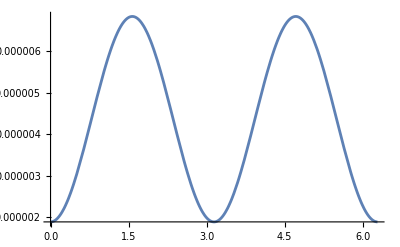

```mathematica
Plot[Penalty[ϕ,zetatest,deltatest],{ϕ,0,2*Pi}]
```

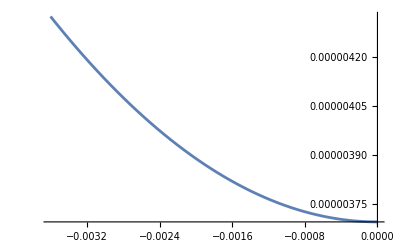

```mathematica
Plot[Penalty[phitest,ζ,deltatest],{ζ,2*zetatest,0}]
```

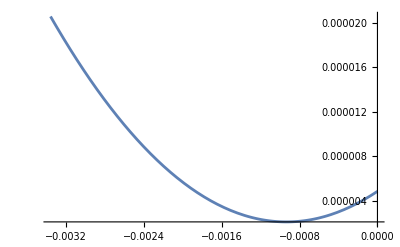

```mathematica
Plot[Penalty[phitest,zetatest,δ],{δ,2*deltatest,0}]
```

```mathematica
incs=100;
Table[Penalty[2*Pi*ii/incs,zetatest,deltatest],{ii,0,incs}]
```

{0.0000137219,0.0000124861,0.0000112697,0.0000100918,8.97105×10^-6,7.92505×10^-6,6.97032×10^-6,6.12193×10^-6,5.39324×10^-6,4.79576×10^-6,4.3389×10^-6,4.02987×10^-6,3.87355×10^-6,3.8724×10^-6,4.02643×10^-6,4.33322×10^-6,4.78793×10^-6,5.3834×10^-6,6.11021×10^-6,6.95693×10^-6,7.91018×10^-6,8.95495×10^-6,0.0000100747,0.0000112519,0.0000124679,0.0000137035,0.0000149393,0.0000161557,0.0000173336,0.0000184543,0.0000195003,0.0000204551,0.0000213035,0.0000220321,0.0000226296,0.0000230865,0.0000233955,0.0000235518,0.000023553,0.000023399,0.0000230922,0.0000226375,0.000022042,0.0000213152,0.0000204685,0.0000195152,0.0000184704,0.0000173506,0.0000161735,0.0000149575,0.0000137219,0.0000124861,0.0000112697,0.0000100918,8.97105×10^-6,7.92505×10^-6,6.97032×10^-6,6.12193×10^-6,5.39324×10^-6,4.79576×10^-6,4.3389×10^-6,4.02987×10^-6,3.87355×10^-6,3.8724×10^-6,4.02643×10^-6,4.33322×10^-6,4.78793×10^-6,5.3834×10^-6,6.11021×10^-6,6.95693×10^-6,7.91018×10^-6,8.95495×10^-6,0.0000100747,0.0000112519,0.0000124679,0.0000137035,0.0000149393,0.0000161557,0.0000173336,0.0000184543,0.0000195003,0.0000204551,0.0000213035,0.0000220321,0.0000226296,0.0000230865,0.0000233955,0.0000235518,0.000023553,0.000023399,0.0000230922,0.0000226375,0.000022042,0.0000213152,0.0000204685,0.0000195152,0.0000184704,0.0000173506,0.0000161735,0.0000149575,0.0000137219}